```mathematica
solution = DSolve[y'[t]==((t-1)/t)*y[t], y[t], t]
```

{{y[t]→(ⅇ^t C[1])/t}}

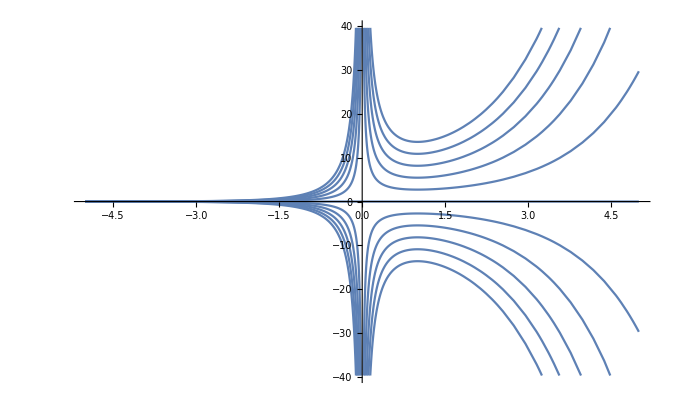

```mathematica
f[t_]=y[t]/. solution⟦1⟧

F[t_]=Table[f[t]/.C[1]->j, {j, -5, 5}]

Plot[{F[t]}, {t, -5, 5}]
```